```mathematica
μSub = p -> (μ-1)/(μ+1);
```

```mathematica
RegPower[x_,α_,ϵ_] := (x x*+ ϵ)^(α/2) E^(I Arg[x] α);
```

```mathematica
θsol =Pi/2 + FullSimplify[(Pi/(γ(p-1))Integrate[(κ^2 v^(-2μ) + v^2)/v,{v, 1, v}])/.μSub, v>1]
```

π/2-(π v^(-2 μ) (1+μ) (-κ^2+v^(2 μ) (κ^2+(-1+v^2) μ)))/(4 γ μ)

```mathematica
π/2-(π(1+μ) (-κ^2 v^(-2 μ)  + (κ^2+(-1+v^2) μ)))/(4 γ μ)
```

π/2-(π (1+μ) (κ^2-v^(-2 μ) κ^2+(-1+v^2) μ))/(4 γ μ)

```mathematica
KappaEq=( θsol==0)
```

π/2-(π v^(-2 μ) (1+μ) (-κ^2+v^(2 μ) (κ^2+(-1+v^2) μ)))/(4 γ μ)==0

```mathematica
Solve[KappaEq,κ][[2]]
```

{κ→(√(-1+v^2-2 γ-μ+v^2 μ))/(√(-1+v^(-2 μ)-1/μ+v^(-2 μ)/μ))}

```mathematica
κ2sol =FullSimplify[(κ/.Solve[KappaEq/.{v->v2},κ][[1]])^2,{μ >0, μ < 1, v2>1}]
```

-(v2^(2 μ) μ (-1-2 γ-μ+v2^2 (1+μ)))/((-1+v2^(2 μ)) (1+μ))

```mathematica
γcrit[μ_,  v2_] :=γ/.Solve[-1-2 γ-μ+v2^2 (1+μ)==0,γ][[1]]//FullSimplify
```

```mathematica
γcrit[μ,  v2]
```

1/2 (-1+v2^2) (1+μ)

```mathematica
κsol[a_,b_,c_] := Sqrt[κ2sol/.{μ->a, γ->b ,v2->c}]
```

```mathematica
κsol[μ,γ,v2]
```

√(-(v2^(2 μ) μ (-1-2 γ-μ+v2^2 (1+μ)))/((-1+v2^(2 μ)) (1+μ)))

```mathematica
test =FullSimplify[(1/(2(p-1))Integrate[(κ v^(-μ) - I v)/v,v])/.μSub]
```

(v^-μ (1+μ) (κ+ⅈ v^(1+μ) μ))/(4 μ)

```mathematica
μ=.;v2=.; κ=.;
```

```mathematica
CC =((1+μ) (κ (v^-μ-1)+ⅈ (v -v2)μ))/(4 μ)
```

((1+μ) ((-1+v^-μ) κ+ⅈ (v-v2) μ))/(4 μ)

```mathematica
Surf[μ_,γ_,v2_] :=
Module[{κ,XY,ϵ=0.00001},
κ = κsol[μ,γ,v2];
Print[" κ = ", κ];
XY[v_] := ((1+μ) (κ (v^-μ-1)+ⅈ (v -v2)μ))/(4 μ);
ParametricPlot[
Module[{X,Y},
{X,Y}= ReIm[XY[v]];
{{X,Y},{-X,Y},{X,-Y},{-X,-Y}}
], {v,1,v2},PlotStyle->{Red,Thick},PlotLabel->TraditionalForm[{Symbol["μ"]==μ ,Symbol["γ"]==γ ,Subscript[Symbol["v"],2]==v2}],
LabelStyle->{FontFamily->"Latin Modern Roman"}
]
];
```

```mathematica
γcrit[0.5,2]
```

2.25

κ = 1.73205

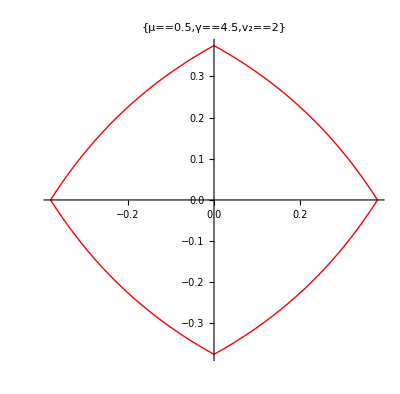

```mathematica
Surf[0.5,2 γcrit[0.5,2],2]
```

```mathematica
ThetaSol[ μ_,γ_,v2_,v_] :=
Module[{ κ},
κ = κsol[μ,γ,v2];
-(π  (1+μ) (κ^2(v2^(-2 μ) -v^(-2 μ))+  (-v2^2+v^2) μ))/(4 γ μ)
];
```

```mathematica
ThetaPlot[μ_,γ_,v2_] :=
Module[{lab, axlab},
Print["thetasol(V2) " , ThetaSol[μ,γ,v2,v2]];
Print["thetasol(1) " , ThetaSol[ μ,γ,v2,1]];
lab =TraditionalForm[{Symbol["μ"]==μ,Symbol["γ"]==γ,Subscript[Symbol["v"],2]==v2}];
ParametricPlot[
{v, ThetaSol[ μ,γ,v2,v]/Pi},{v,1, v2},
AxesLabel->{v,θ/Pi},
PlotLabel->lab, PlotRange->All]
];
```

thetasol(V2) 0.

thetasol(1) 1.5708

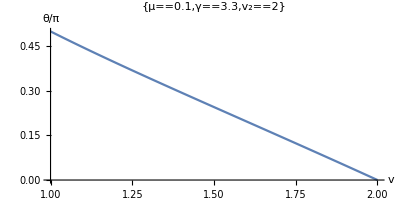

```mathematica
ThetaPlot[0.1,2 γcrit[0.1,2],2]
```

```mathematica
CFrac[F_,x_, L_]:=
Module[{f0,f, CC={}, l },
l = L;
f = F;
While[l >0 ,
f0 = f/.x->0;
AppendTo[CC,f0];
f -= f0;
If[f==0,Break[]];
l-=1;
f =Normal[Series[x/f ,{x,0,l}]];
];
CC
];
```

```mathematica
FromCFrac[Coeffs_, x_,ϵ_:10^(-32)]:=
Module[{f},
For[ n=Length[Coeffs];f=Coeffs[[n]], n>1,n-=1,
f =Coeffs[[n-1]] +N[ x f*/(f f*+ ϵ)];
];
f
];
```

```mathematica
SelfConsistencyEquation[μ_?NumericQ,γ_?NumericQ,  v2_?NumericQ]:=
Module[
{
κ,u1,u2,u,θ,ω,X,V,C1, CI,  CCReal,ϵ=0.0000001
},
κ = κsol[μ,γ,v2];
u1 = κ;
u2 = κ RegPower[v2,-μ,ϵ];
u[v_?NumericQ] := κ RegPower[v,-μ,ϵ];
θ[v_?NumericQ] :=-(π  (1+μ) (κ^2(v2^(-2 μ) -v^(-2 μ))+  (-v2^2+v^2) μ))/(4 γ μ);
ω[v_?NumericQ] := Exp[I θ[v]];
X[v_?NumericQ] :=((1+μ) ((-1+v^-μ) κ+ⅈ (v-v2) μ))/(4 μ);
C1 = ((1+μ) κ (v2^-μ-1))/(4 μ);
CI= ((1+μ) (v2-1))/4;
((μ+1)/(2  CI)NIntegrate[
Block[{ U,X0,ω0},
U = u[v]+I v;
X0 =X[v];
ω0=ω[v];
Abs[U]^2  Re[X0 ω0* RegPower[ω0^2+1,-1,ϵ]] ],{v,1,v2},
Method->"LocalAdaptive",MaxRecursion->100,AccuracyGoal->5,WorkingPrecision->MachinePrecision])/
((μ+1)/(2  C1)NIntegrate[
Block[{ U,X0,ω0},
U = u[v]+I v;
X0 =X[v];
ω0=ω[v];
Abs[U]^2  Re[X0 ω0* RegPower[ω0^2-1,-1,ϵ]] ],{v,1,v2},
Method->"LocalAdaptive",MaxRecursion->100,AccuracyGoal->5,WorkingPrecision->MachinePrecision])
-1
];
```

```mathematica
γ=.;
```

```mathematica
SelfConsistencyEquation[1,2 γcrit[1,2],2]
```

-0.0272985

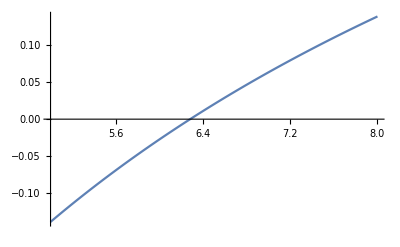

```mathematica
Plot[SelfConsistencyEquation[1,γ,2],{γ,5 ,8}]
```

```mathematica
GetGamma[μ_, v2_ , γ0_]:= 
Module[{x },
γ/.FindRoot[SelfConsistencyEquation[μ,γ,v2],{γ,Max[1.1γcrit[μ,v2],0.5 γ0],1.5γ0}]
];
```

```mathematica
ggg =GetGamma[1, 2, 6]
```

6.28116

```mathematica
"
```

```mathematica
SelfConsistencyEquation[1,ggg,2]
```

4.44089×10^-16

```mathematica
SizeEquation[μ_?NumericQ,v2_?NumericQ]:=
Module[
{
κ,u1,u2,u,θ,ω,X,V,C1,γ, CI,  CCReal,ϵ=0.0000001
},
γ = GetGamma[μ,v2,2 γcrit[μ,v2]];
κ = κsol[μ,γ,v2];
u1 = κ;
u2 = κ RegPower[v2,-μ,ϵ];
u[v_?NumericQ] := κ RegPower[v,-μ,ϵ];
θ[v_?NumericQ] :=-(π  (1+μ) (κ^2(v2^(-2 μ) -v^(-2 μ))+  (-v2^2+v^2) μ))/(4 γ μ);
ω[v_?NumericQ] := Exp[I θ[v]];
X[v_?NumericQ] :=((1+μ) ((-1+v^-μ) κ+ⅈ (v-v2) μ))/(4 μ);
C1 = ((1+μ) κ (v2^-μ-1))/(4 μ);
CI= ((1+μ) (v2-1))/4;
(-(μ+1)/(γ  CI)NIntegrate[
Block[{ U,X0,ω0},
U = u[v]+I v;
X0 =X[v];
ω0=ω[v];
Abs[U]^2  Re[X0 ω0* RegPower[ω0^2+1,-1,ϵ]] ],{v,1,v2},
Method->"LocalAdaptive",MaxRecursion->100,AccuracyGoal->5,WorkingPrecision->MachinePrecision])
];
```

```mathematica
FindRoot[SizeEquation[1,v2]==1,{v2,1.5,5}]
```

{v2→3.49209}

```mathematica
GetCirculationGammaV2[μ_?NumericQ, v2_?NumericQ,γ0_:50]:=
Module[
{
γ,κ,u1,u2,u,θ,ω,X,V,A1,B1,ϵ=0.0000001
},
γ = GetGamma[μ,v2 , γ0];
κ = κsol[μ,γ,v2];
u1 = κ;
u2 = κ RegPower[v2,-μ,ϵ];
u[v_?NumericQ] := κ RegPower[v,-μ,ϵ];
θ[v_?NumericQ] :=-(π  (1+μ) (κ^2(v2^(-2 μ) -v^(-2 μ))+  (-v2^2+v^2) μ))/(4 γ μ);
ω[v_?NumericQ] := Exp[I θ[v]];
X[v_?NumericQ] :=((1+μ) ((-1+v^-μ) κ+ⅈ (v-v2) μ))/(4 μ);
A1 = NIntegrate[
With[{U = u[v]+I v,ω0=ω[v]},
Abs[U]^2/v Im[U ω0]],
{v,1,v2},
Method->{"GlobalAdaptive","SymbolicProcessing"->0,"MaxErrorIncreases"->2000},MaxRecursion->20,WorkingPrecision->60,PrecisionGoal->8,AccuracyGoal->Infinity
];
B1 = NIntegrate[
With[{U = u[v]+I v,X0 =X[v],ω0=ω[v]},
Abs[U]^2/v Re[X0 ω0^(-1)]],
{v,1,v2},
(* {"Method","MinRecursion","MaxRecursion","MaxPoints","Partitioning","SingularityDepth","SingularityHandler","InitialEstimateRelaxation","SymbolicProcessing"}*)
Method->{"GlobalAdaptive","SymbolicProcessing"->0,"MaxErrorIncreases"->2000},MaxRecursion->20,WorkingPrecision->60,PrecisionGoal->8,AccuracyGoal->Infinity
];
{-(1 + μ)^2/(γ^3)A1 B1, γ, v2}
];
```

```mathematica
GetGamma[1,10 ,2 γcrit[1,10]]
```

223.742

```mathematica
GetCirculationGammaV2[1,10,2 γcrit[1,10]]
```

{0.16421,223.742,10}

```mathematica
γcrit[0.1,2]
```

1.65

```mathematica
GetGamma[0.1, 2 , 2 γcrit[0.1,2]]
```

4.85586

```mathematica
gdata =ParallelTable[SizeEquation[1,v2 ],{v2,2,5,0.1}]
```

{0.675361,0.697974,0.720446,0.742782,0.764986,0.787064,0.809019,0.830855,0.852575,0.874184,0.895683,0.917077,0.938369,0.959561,0.980656,1.00166,1.02257,1.04339,1.06412,1.08477,1.10534,1.12583,1.14625,1.16659,1.18685,1.20705,1.22718,1.24724,1.26723,1.28717,1.30704}

```mathematica
GData[NP_, Nreps_, vmin_:1.5, vmax_:3]:= 
Module[{ tbl = {}, vstep, pstep,  vguess},
pstep = 1/NP;
tbl = ParallelTable[
Module[{γ0=25 ,γ1=25, rdata={},vdata={}, G,a,b,c,tmp},
a = vmin;
b = vmax;
γ0 = N[2 γcrit[μ,vmax]];
For[subs=1, subs < Nreps,subs+=1,
(*Print["γ0= ", γ0, ", a= ", a, ", b = " ,b];*)
c = N[(a+ b)/2];
G  = SizeEquation[μ,c ];
γ1 = GetGamma[μ,c,γ0];
(*Print[{G,γ1,c}];*)
If[G >1 ,
b = c;
γ0= γ1,
If[G <1,
a = c;
γ0= γ1
]
];
vguess = (a + b)/2;
];
γ1 = GetGamma[μ,vguess , γ0];
(*Print[{N[μ],vguess, γ1 , G}];*)
vguess + I γ1 
],{μ,1,pstep,-pstep}];
ListInterpolation[Reverse[tbl],{{pstep,1}}]
];
```

```mathematica
gd = GData[100,20, 3,4];
```

```mathematica
gd[0.5]
```

3.34348+18.3797 ⅈ

```mathematica
gd[1]
```

3.49209+23.7633 ⅈ

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

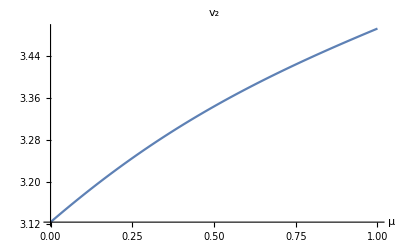

```mathematica
Plot[Re[gd[μ]],{μ,0,1},  PlotLabel->Subscript[Symbol["v"],2], AxesLabel->{μ,None}]
```

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

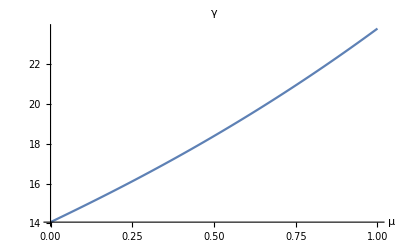

```mathematica
Plot[Im[gd[μ]],{μ,0,1},  PlotLabel->Symbol["γ"], AxesLabel->{μ,None}]
```

```mathematica
(**)
```

```mathematica
UniqueSurf[μ_] :=
Module[{γ,v2},
 {v2 , γ} = ReIm[gd[μ]];
Surf[μ,γ,v2]
];
```

κ = 3.58619

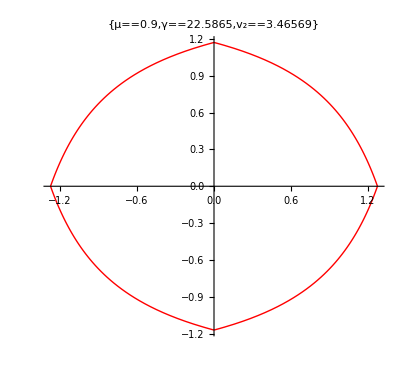

```mathematica
UniqueSurf[0.9]
```

κ = 2.94971

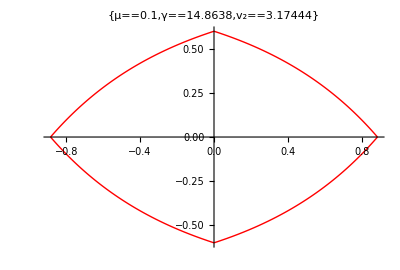

```mathematica
UniqueSurf[0.1]
```

```mathematica
Tubes[μ1_, μ2_] :=
Module[{},
P1 = UniqueSurf[μ1];
P2 =UniqueSurf[μ2];
Grid[{
{Show[P1,PlotRange->All,ImageSize->{240,400},AspectRatio->Full],Show[P2,PlotRange->All,ImageSize->{240,400},AspectRatio->Full]}
}]
];
```

```mathematica
p = .;
```

κ = 2.94971

κ = 3.58619

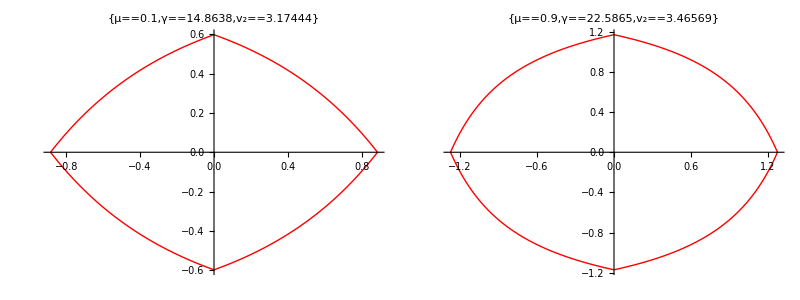

```mathematica
Tubes[0.1,0.9]
```

```mathematica
CC=.;
```

```mathematica
ComplexMaps[μ_, M_, L_]:=
Module[{ϵ = 10^(-12),v2, γ, κ, u2, CC,V, C1, C2, Atable,Btable},
{v2 , γ} = ReIm[gd[μ]];
Print["γ =", γ, " v2 = ", v2];
labV =TraditionalForm[{Symbol["V"],Symbol["μ"]==μ,Symbol["γ"]==γ,Subscript[Symbol["v"],2]==v2}];
labC=TraditionalForm[{Symbol["C"],Symbol["μ"]==μ,Symbol["γ"]==γ,Subscript[Symbol["v"],2]==v2}];
κ = κsol[μ,γ,v2];
u1 = κ;
u2 = κ RegPower[v2,-μ,ϵ];
u[v_?NumericQ] := κ RegPower[v,-μ,ϵ];
θ[v_?NumericQ] :=-(π  (1+μ) (κ^2(v2^(-2 μ) -v^(-2 μ))+  (-v2^2+v^2) μ))/(4 γ μ);
ω[v_?NumericQ] := Exp[I θ[v]];
X[v_?NumericQ] :=((1+μ) ((-1+v^-μ) κ+ⅈ (v-v2) μ))/(4 μ);
C1 = ((1+μ) κ (v2^-μ-1))/(4 μ);
CI= ((1+μ) (v2-1))/4;
pV = ComplexPlot3D[V[ξ],{ξ,-L-L I,L+ L I}, 
Exclusions->{Abs[ξ]==1},
ExclusionsStyle->Black,
PlotLabel->labV,PlotLegends->None,LabelStyle->{FontFamily->"Latin Modern Roman"},ImageSize->Medium,
PlotRange->{0,4}];
Btable = 
ParallelTable[
NIntegrate[
With[{U = u[v]+I v,X0 =X[v],ω0=ω[v]},
Abs[U]^2/v Re[X0 ω0^(2 n -3)]],
{v,1,v2},
(* {"Method","MinRecursion","MaxRecursion","MaxPoints","Partitioning","SingularityDepth","SingularityHandler","InitialEstimateRelaxation","SymbolicProcessing"}*)
Method->{"GlobalAdaptive","SymbolicProcessing"->0,"MaxErrorIncreases"->2000},MaxRecursion->20,WorkingPrecision->60,PrecisionGoal->8,AccuracyGoal->Infinity
],{n,M}];
BtoC = CFrac[Sum[Btable[[k]] x^k,{k,M}],x,M];
CC[ξ_?NumericQ] :=-(1+μ) ξ^3/(γ)  FromCFrac[BtoC,1/ξ^2];
pC = ComplexPlot3D[CC[ξ],{ξ,-L-L I,L + L I}, 
Exclusions->{Abs[ξ]==1 },
ExclusionsStyle->Black,
PlotLabel->labC,PlotLegends->Automatic,LabelStyle->{FontFamily->"Latin Modern Roman"},ImageSize->Medium,
PlotRange->{0,2}];
V[ξ_?NumericQ] :=γ/(2 Pi I ξ CC'[ξ]);
pV = ComplexPlot3D[V[ξ],{ξ,-L-L I,L + L I}, 
Exclusions->{Abs[ξ]==1 },
ExclusionsStyle->Black,
PlotLabel->labC,PlotLegends->Automatic,LabelStyle->{FontFamily->"Latin Modern Roman"},ImageSize->Medium,
PlotRange->{0,8}];
Grid[{{pV ,pC}}]
];
```

```mathematica
CircleWithArrows[R_] :=
Show[
Table[With[{pt = ReIm[R Exp[I θ]]},
Graphics[{
Red,
Arrowheads[0.01],
Arrow[{pt,RandomPoint[Circle[pt,R/10]]}]
}]
],{θ,-Pi,Pi,Pi/120}]
]
```

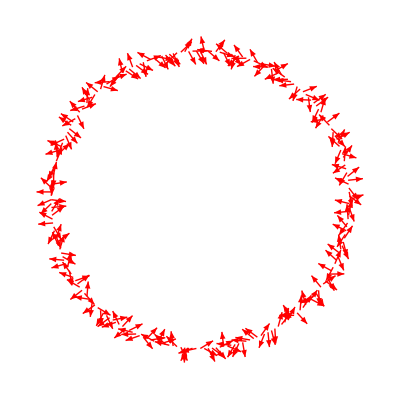

```mathematica
CircleWithArrows[1]
```

```mathematica
ClearAll[v,v2, R0, μ,MakeFlow];
```

```mathematica
MakeFlow[μ_,M_,L_,K_, NumR_, Numθ_, R0_]:=
Module[{ϵ = 10^(-12),v2,v, γ, κ, u1,u2,xmax, ymax, labV,Atable, Btable, AtoC, BtoC, V,CC, RegV},
{v2 , γ} = ReIm[gd[μ]];
Print["γ =", γ];
labV =TraditionalForm[{Symbol["V"],Symbol["μ"]==μ,Symbol["R0"]==R0,Symbol["Γ"]==γ R0^2}];
κ = κsol[μ,γ,v2];
u1 = κ;
u2 = κ RegPower[v2,-μ,ϵ];
u[v_?NumericQ] := κ RegPower[v,-μ,ϵ];
θ[v_?NumericQ] :=-(π  (1+μ) (κ^2(v2^(-2 μ) -v^(-2 μ))+  (-v2^2+v^2) μ))/(4 γ μ);
ω[v_?NumericQ] := Exp[I θ[v]];
X[v_?NumericQ] :=((1+μ) ((-1+v^-μ) κ+ⅈ (v-v2) μ))/(4 μ);
xmax =R0 Abs[(κ - u2)](1 + μ)/(4 μ);
ymax =R0 Abs[(v2-1)](1+ μ)/4;
Print ["{xmax, ymax} =", {xmax,ymax}];
RegV[x_,y_]:={2 μ/(1+μ)x,-2/(μ+1)y};
Btable = 
ParallelTable[
NIntegrate[
With[{U = u[v]+I v,X0 =X[v],ω0=ω[v]},
Abs[U]^2/v Re[X0 ω0^(2 n -3)]],
{v,1,v2},
(* {"Method","MinRecursion","MaxRecursion","MaxPoints","Partitioning","SingularityDepth","SingularityHandler","InitialEstimateRelaxation","SymbolicProcessing"}*)
Method->{"GlobalAdaptive","SymbolicProcessing"->0,"MaxErrorIncreases"->2000},MaxRecursion->20,WorkingPrecision->60,PrecisionGoal->8,AccuracyGoal->Infinity
],{n,M}];
BtoC = CFrac[Sum[Btable[[k]] x^k,{k,M}],x,M];
CC[ξ_?NumericQ] :=-R0(1+μ) ξ^3/(γ)  FromCFrac[BtoC,1/ξ^2];
V[ξ_?NumericQ] :=γ R0^2/(2 Pi I ξ CC'[ξ]);
(*VDirect[ξ_?NumericQ]:= -R0   ξ(1 + μ)/(2γ) 
NIntegrate[
With[{U = u[v]+I v,ω0=ω[v]},
  Abs[U]^2/v (U ω0 RegPower[ω0^2-ξ^2,-1,ϵ]- U*ω0*RegPower[ω0*^2-ξ^2,-1,ϵ])],
{v,1,v2},
Method->"LocalAdaptive",MaxRecursion->100,AccuracyGoal->5,WorkingPrecision->MachinePrecision];
CCDirect[ξ_?NumericQ]:=R0(1 + μ)ξ^3/(2γ)
NIntegrate[
With[{U = u[v]+I v,X0 =X[v],ω0=ω[v]},
Abs[U]^2/v (X0 ω0*RegPower[ω0^2-ξ^2,-1,ϵ] + X0*ω0 RegPower[ω0*^2-ξ^2,-1,ϵ])],
{v,1,v2},
Method->"LocalAdaptive",MaxRecursion->100,AccuracyGoal->5,WorkingPrecision->MachinePrecision];*)
Velocities[NR_, Nθ_] :=
Module[{vtr},
vtr = ParallelTable[With[{η= Sqrt[1+ϵ+ r^2] Exp[I α]},
{ReIm[CC[η]], RegV[Re[η],Im[η]]+ReIm[ Conjugate[V[η]]]}],{r,0,K,1/NR},{α,-Pi,Pi,Pi/Nθ}];
Flatten[vtr,1]
];
loop = ParametricPlot[
Module[{Xp,Yp},
{Xp,Yp}= ReIm[X[v]];
{{Xp,Yp},{-Xp,Yp},{-Xp,-Yp},{Xp,-Yp}}
], {v,1,v2},PlotStyle->{Red,Thick},Axes->False];

Test[R_] :=  Im[R]^2/(R R*);
Outside[R_]:=
Module[{t, v0},
t= Test[R];
v0 = (vv/.FindRoot[ Test[X[vv]]==t,{vv,1,v2}]);
Abs[R]> Abs[X[v0]]
];
Flow[NR_, Nθ_]:=
Module[{pts,Vel},
Vel= Velocities[NR,Nθ];
Print[" done velocities"];
Show[
{
ListStreamPlot[
Vel,
RegionFunction->Function[{x,y},Outside[x+I y]&&Abs[x+I y]<L],
RegionFillingStyle->None,
StreamScale->Tiny,
StreamColorFunction->None,
PlotLabel->labV,
LabelStyle->{FontFamily->"Latin Modern Roman"},
ImageSize->Large
,Axes->False,Frame->False, PlotRange->Full
],
StreamPlot[RegV[x,y],
{x,-xmax,xmax},{y,-ymax,ymax},
RegionFunction->Function[{x,y,z},!Outside[x + I y]],
RegionFillingStyle->None,
StreamScale->Tiny,
StreamColorFunction->None,
PlotLabel->None,
ImageSize->Large
,Axes->False
],
loop(*,
CircleWithArrows[R0]*)
},Boxed->False,Axes->False
]
];
Flow[NumR, Numθ]
];
```

```mathematica
p = .
```

```mathematica
p = .; γ=.;
```

```mathematica
ComplexMaps[0.5, 40, 2]
```

γ =18.3797 v2 = 3.34348

-Graphics3D- | -Graphics3D-

```mathematica
(*μ_,M_,L_,K_, NumR_, Numθ_, R0_*)
```

γ =18.3797

{xmax, ymax} ={1.08643,0.878805}

done velocities

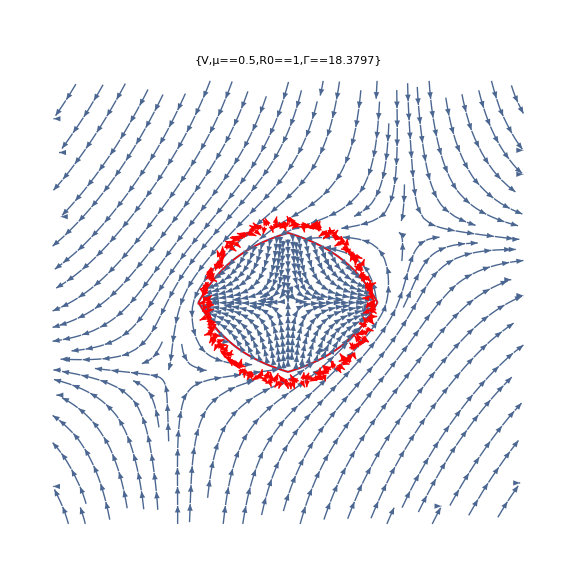

```mathematica
MakeFlow[0.5,32,4,3,10, 512,1]
```

```mathematica
-
```

```mathematica
DI[κ_,μ_,v2_] := Evaluate[Assuming[{κ>0,v2>1,μ>0, μ < 1},Integrate[(κ^2 v^(- 2 μ) + v^2)^(3/2)/v, {v,1,v2}]]]
```

```mathematica
DI[κ,μ,v2]
```

1/(9 μ)v2^(-3 μ) κ (v2^(3 μ) (1-2 μ+κ^2 (4+μ)) Hypergeometric2F1[-1/2,-(3 μ)/(2+2 μ),(2-μ)/(2+2 μ),-1/κ^2]+(-κ^2 (4+μ)+v2^(2+2 μ) (-1+2 μ)) Hypergeometric2F1[-1/2,-(3 μ)/(2+2 μ),(2-μ)/(2+2 μ),-v2^(2+2 μ)/κ^2]-(1+μ) (v2^(3 μ) (1+κ^2) Hypergeometric2F1[1/2,-(3 μ)/(2+2 μ),(2-μ)/(2+2 μ),-1/κ^2]-(v2^(2+2 μ)+κ^2) Hypergeometric2F1[1/2,-(3 μ)/(2+2 μ),(2-μ)/(2+2 μ),-v2^(2+2 μ)/κ^2]))

```mathematica
F[μ_] := 
Module[{ϵ = 10^(-12),v2,u1,u2, γ,p, κ},
{v2 , γ} = ReIm[gd[μ]];
κ = κsol[μ,γ,v2];
Sqrt[(1-μ^2)/Pi]/(2 γ^(3/2)) DI[κ,μ,v2]
];
```

```mathematica
F[0.5]
```

0.121776

InterpolatingFunction::dmval: Input value {0.0000204284} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

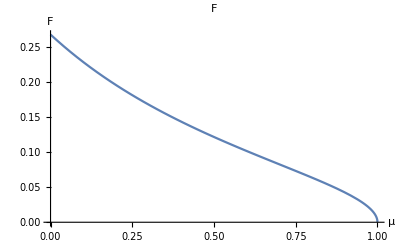

```mathematica
Plot[F[μ],{μ,0,1-0.00001}, PlotLabel->Symbol["F"], AxesLabel->{μ,F}]
```

```mathematica
Pr[r_,q_] := 4 Sqrt[3/Pi] q^4 Abs[1-9 r^2] Exp[- q^2 (1 + 3 r^2)];
```

```mathematica
Pμq[μ_,q_] := (64 E^(-((4 q^2 (1+(-1+μ) μ))/(1+μ)^2)) Sqrt[3/π] q^4 (2-μ) Abs[2 μ-1])/(1+μ)^4
```

```mathematica
ScalingProb[ζ_] :=
NIntegrate[F[μ]Pμq[μ,ζ/F[μ]],{μ,0,0.999999}, Method->"GlobalAdaptive"];
```

```mathematica
ScalingProb[0.001]
```

4.16254×10^-7

```mathematica
Assuming[{f>0,μ >0, μ < 1},Integrate[f Pμq[μ,ζ/f] ζ,{ζ,0,Infinity}]]
```

-(f^3 √(3/π) (-2+μ) (1+μ)^2 Abs[1-2 μ])/(1+(-1+μ) μ)^3

```mathematica
Assuming[{f>0,μ >0, μ < 1},Integrate[f Pμq[μ,ζ/f] ,{ζ,0,Infinity}]]
```

-(3 √3 f^2 (-2+μ) (1+μ) Abs[1-2 μ])/(4 (1+(-1+μ) μ)^(5/2))

```mathematica
II1 =NIntegrate[-(F[μ]^3 √(3/π) (-2+μ) (1+μ)^2 Abs[1-2 μ])/(1+(-1+μ) μ)^3,{μ,0,0.9999}, Method->"GlobalAdaptive"]
```

0.0086112

```mathematica
II2 =NIntegrate[-(3 √3 F[μ]^2 (-2+μ) (1+μ) Abs[1-2 μ])/(4 (1+(-1+μ) μ)^(5/2)),{μ,0,0.9999},Method->"GlobalAdaptive"]
```

0.0461303

```mathematica
Meanζ = II1/II2
```

0.186671

```mathematica
ScalingProb[Meanζ]
```

0.271282

```mathematica
sptbl = ParallelTable[Log[ScalingProb[ζ]],{ζ, 0.01Meanζ, 3 Meanζ,0.01}];
```

```mathematica
SPinterp =ListInterpolation[sptbl,{{0.01Meanζ, 3 Meanζ}}]
```

InterpolatingFunction[…]

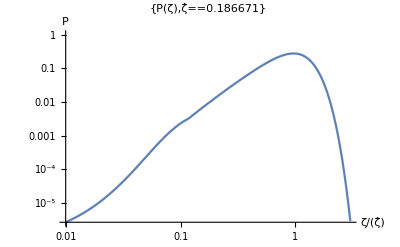

```mathematica
LogLogPlot[Exp[SPinterp[x Meanζ]],{x,0.01, 3 },PlotLabel->{P[ζ], ζ̂ ==Meanζ},AxesLabel->{ζ/ζ̂ ,P}]
```

```mathematica
|
```

```mathematica
Meanζ/Sqrt[20 Pi^3]
```

0.00749613

```mathematica
gd[0.5]
```

3.34348+18.3797 ⅈ

```mathematica
Sol[μ_] := 
Module[{v2, γ, κ, XY},
{v2 , γ} = ReIm[gd[μ]];
Print[{v2 , γ}];
κ = κsol[μ,γ,v2];
{-(π  (1+μ) (κ^2(v2^(-2 μ) -#^(-2 μ))+  (-v2^2+#^2) μ))/(4 γ μ)&,
((1+μ) (κ (#^-μ-1)+ⅈ (# -v2)μ))/(4 μ)&,
v2}
];
```

```mathematica
Surf[sol_,R0_,z_,θ_,ρ_]:=
Module[{ξ,XY,C0, θs,v2, v0, v},
{θs, XY, v2} = sol;
C0 =If[ Abs[θ ]< Pi/2,
v0 = (v/.FindRoot[θs[v]==Abs[θ ],{v,1,v2}]);
(*Print["θ= ", θ, " v0= ", v0];*)
If[θ >0,XY[v0],Conjugate[XY[v0]]],
v0 = (v/.FindRoot[θs[v]==Pi -Abs[θ ],{v,1,v2}]);
If[θ >0,-Conjugate[XY[v0]],-XY[v0]]];
ξ=R0 E^(I ρ) C0;
Join[ReIm[ξ],{z}]
];
```

```mathematica
ClearAll[Noodle,MakeSols];
MakeSols[μ1_,μ2_]:={Sol[μ1],Sol[μ2]};
Noodle[{sol1_,sol2_},l_,λ_]:=
Module[{R0,T0},
ParametricPlot3D[
Module[{z1=Sin[ω1 t],z2=Sin[ω2 t]},
(1-t) Surf[sol1,t,t l,θ,λ t]+t Surf[sol2,t,t l,θ,λ t]],
{θ,-Pi,Pi},{t,0,1},Mesh->None,Boxed->False,Axes->False,MaxRecursion->5,PlotRange->All]];
```

```mathematica
sols=MakeSols[0.01,0.99];
```

{3.12806,14.1461}

{3.4895,23.6432}

```mathematica
sols
```

{{-(π (1+0.01) (κ$1965991^2 (v2$1965991^(-2 0.01)-#1^(-2 0.01))+(-v2$1965991^2+#1^2) 0.01))/(4 γ$1965991 0.01)&,((1+0.01) (κ$1965991 (#1^-0.01-1)+ⅈ (#1-v2$1965991) 0.01))/(4 0.01)&,3.12806},{-(π (1+0.99) (κ$1965992^2 (v2$1965992^(-2 0.99)-#1^(-2 0.99))+(-v2$1965992^2+#1^2) 0.99))/(4 γ$1965992 0.99)&,((1+0.99) (κ$1965992 (#1^-0.99-1)+ⅈ (#1-v2$1965992) 0.99))/(4 0.99)&,3.4895}}

```mathematica
Surf[sols[[2]],1,1,Pi/4,1]
```

{0.248811,-1.14695,1}

```mathematica
Noodle[sols,5,Pi]
```

-Graphics3D-

```mathematica
CirculationPlot[μ_]:=
Module[{ξ,γ,XY,C0, θs,v2, v0, v},
{v2 , γ} = ReIm[gd[μ]];
{θs, XY, v2} = Sol[μ];
C0[θ_] :=If[ Abs[θ ]< Pi/2,
v0 = (v/.FindRoot[θs[v]==Abs[θ ],{v,1,v2}]);
(*Print["θ= ", θ, " v0= ", v0];*)
If[θ >0,XY[v0],Conjugate[XY[v0]]],
v0 = (v/.FindRoot[θs[v]==Pi -Abs[θ ],{v,1,v2}]);
If[θ >0,-Conjugate[XY[v0]],-XY[v0]]];
ParametricPlot[{α,γ/(2 Pi)Arg[C0[α]]},{α,-Pi,Pi},PlotLabel->{"Circulation", Symbol["μ"]==μ}, Axes->{α,Γ},AspectRatio->1]
];
```

{3.34348,18.3797}

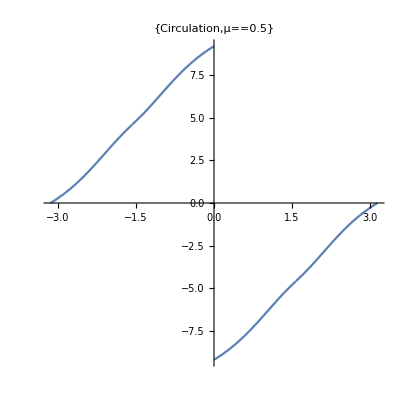

```mathematica
CirculationPlot[0.5]
```

```mathematica
TangentGapPlot[μ_] :=
Module[{ξ,γ,XY,C0, θs,v2, v0, κ,v, Vdata, Cdata},
{v2 , γ} = ReIm[gd[μ]];
{θs, XY, v2} = Sol[μ];
κ = κsol[μ,γ,v2];
P1 = ParametricPlot[{κ v^(-μ) ,v},{v,1,v2}, AspectRatio->1];
P2 = ParametricPlot[{κ v^(-μ) ,-v},{v,1,v2}, AspectRatio->1];
P3= ParametricPlot[{-κ v^(-μ) ,v},{v,1,v2}, AspectRatio->1];
P4 = ParametricPlot[{-κ v^(-μ) ,-v},{v,1,v2}, AspectRatio->1];
Show[{P1,P2,P3,P4},PlotRange->All, Axes->False,PlotLabel->{V, Symbol["μ"]==μ}]
];
```

{3.34348,18.3797}

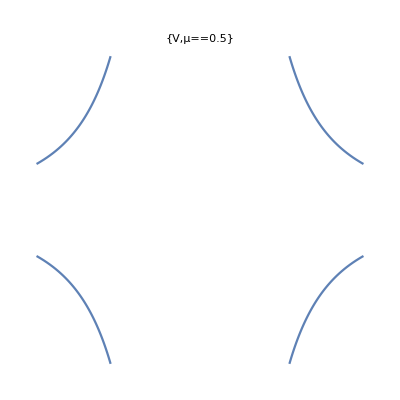

```mathematica
TangentGapPlot[0.5]
```

{3.34348,18.3797}

{3.34348,18.3797}

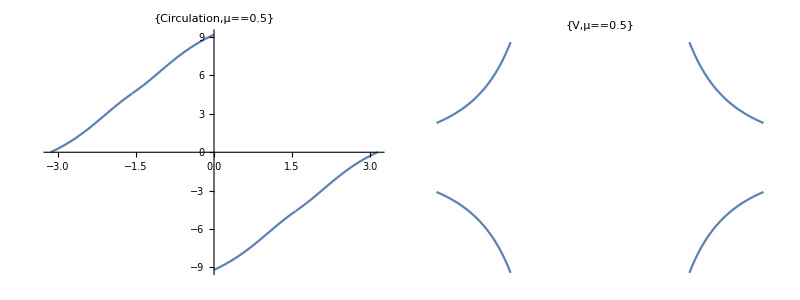

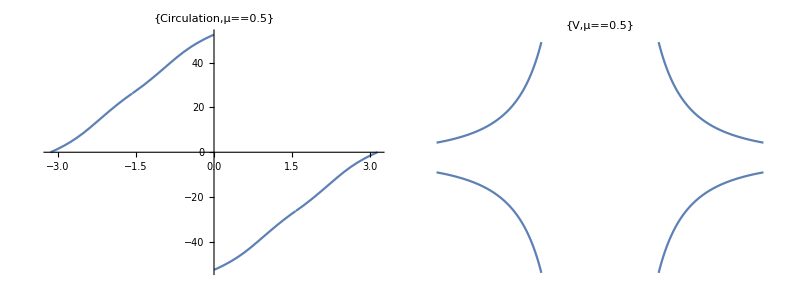

```mathematica
Grid[{{CirculationPlot[0.5],TangentGapPlot[0.5]}}]
```

```mathematica
ClearAll[u, v];
```

```mathematica
TangentGapPolarPlot[μ_] :=
Module[{ξ,γ,XY,C0, θs,v2,u, v0, κ, umax,Reg},
{v2 , γ} = ReIm[gd[μ]];
{θs, XY, v2} = Sol[μ];
κ = κsol[μ,γ,v2];
u[v_] := κ v^(-μ);
P1 = ParametricPlot3D[{Re[XY[v]],Im[XY[v]],t Abs[u[v] + I v]},{v,1,v2},{t,0,1}, Mesh->None,MaxRecursion->5];
P2 = ParametricPlot3D[{Re[XY[v]],-Im[XY[v]],t Abs[u[v] + I v]},{v,1,v2},{t,0,1}, Mesh->None,MaxRecursion->5];
P3 = ParametricPlot3D[{-Re[XY[v]],Im[XY[v]],t Abs[u[v]+ I v]},{v,1,v2},{t,0,1}, Mesh->None,MaxRecursion->5];
P4 = ParametricPlot3D[{-Re[XY[v]],-Im[XY[v]],t Abs[u[v] + I v]},{v,1,v2},{t,0,1}, Mesh->None,MaxRecursion->5];
Show[{P1,P2,P3,P4},PlotRange->All, Axes->True,PlotLabel->{"V Gap", Symbol["μ"]==μ}, AspectRatio->1]
];
```

```mathematica
TangentGapPolarPlot[0.5]
```

{3.34348,18.3797}

-Graphics3D-

```mathematica
CirculationPolarPlot[μ_] :=
Module[{ξ,γ,XY,C0, θs,v2,u, v0, κ, umax,Reg},
{v2 , γ} = ReIm[gd[μ]];
{θs, XY, v2} = Sol[μ];
κ = κsol[μ,γ,v2];
u[v_] = κ v^(-μ);
C0[θ_] :=If[ Abs[θ ]< Pi/2,
v0 = (v/.FindRoot[θs[v]==Abs[θ ],{v,1,v2}]);
(*Print["θ= ", θ, " v0= ", v0];*)
If[θ >0,XY[v0],Conjugate[XY[v0]]],
v0 = (v/.FindRoot[θs[v]==Pi -Abs[θ ],{v,1,v2}]);
If[θ >0,-Conjugate[XY[v0]],-XY[v0]]];
ParametricPlot3D[With[{CC =C0[α]}, {Re[CC],Im[CC],t Arg[CC]}],{α,-Pi,Pi},{t,0,1},PlotLabel->{"Circulation", Symbol["μ"]==μ}, AspectRatio->1, Mesh->None]
];
```

```mathematica
CirculationPolarPlot[0.5]
```

{3.34348,18.3797}

-Graphics3D-

```mathematica
Show[%122,ViewPoint->{1.3,-2.4,2.}]
```

-Graphics3D-

```mathematica
TangentFlowPolarPlot[μ_] :=
Module[{ξ,γ,XY,C0, θs,v2,u, v0, κ, umax,flow},
{v2 , γ} = ReIm[gd[μ]];
{θs, XY, v2} = Sol[μ];
κ = κsol[μ,γ,v2];
flow[v_]:=Re[ (κ v^(-μ) + I v)XY'[v]/θs'[v]];
P1 = ParametricPlot3D[{Re[XY[v]],Im[XY[v]],flow[v]},{v,1,v2}];
P2 = ParametricPlot3D[{Re[XY[v]],-Im[XY[v]], flow[v]},{v,1,v2}];
P3 = ParametricPlot3D[{-Re[XY[v]],Im[XY[v]], flow[v]},{v,1,v2}];
P4 = ParametricPlot3D[{-Re[XY[v]],-Im[XY[v]],flow[v]},{v,1,v2}];
Show[{P1,P2,P3,P4},PlotRange->All, Axes->True,PlotLabel->{"V Gap", Symbol["μ"]==μ}]
];
```

```mathematica
TangentFlowPolarPlot[0.5]
```

{3.34348,18.3797}

-Graphics3D-